```mathematica
𝒲D=DigitCount[#,2,1]&;
computeW[a_,outType_:0]:=Module[{ad,b,genAD,weights,tally,range},
ad=FromDigits[#,2]&/@a;
b=Tuples[{0,1},a//Length];
genAD=Fold[BitXor]/@((Times[ad,#]&)/@b)//Union;
weights= 𝒲D/@genAD;
tally=weights//Tally;
range=Array[{0,0}&,1+Max@(tally[[;;,1]])];
(range[[#+1,1]] = #)&/@ Range[0,(Max@(tally[[;;,1]]))];
(range[[ #[[1]]+1,2 ]]=#[[2]])&/@tally;
Switch[outType,
0,range,
1,{weights,genAD},
2,range[[;;,2]]
]
]
weightsHistorgram = BarChart[#[[;;, 2]], ChartLabels->#[[;;,1]]]&;
```

```mathematica
runOnA[A_]:=Module[{w,dataStr,hist,max},
w=computeW[A];
max=Max[w[[;;,1]] ];
hist=Range[0,max]//Tally;
(hist[[#[[1]]+1,2]]=0)&/@hist;
(hist[[#[[1]]+1,2]]=#[[2]])&/@w;
hist
]
```

```mathematica
genMat[seq_:{3},height_:3,width_:3]:=Module[{l,h=height,m,e,i,j=1},
(* seq =~ {4,3,2,1} *)
h =Max[seq~Join~{h}];
l=Total@seq;
l=Max[l,width];
m=Table[0,{ii,1,h},{jj,1,l}];


For[i=1,i≤ Length@seq,i++,
e=seq[[i]];
If[e==0,Continue[]];
m[[1;;e,j;;j+e-1]]=DiagonalMatrix[Array[1&,e]];
j+=e;
];
m
]
```

```mathematica
genMat[{4,3,3,0,0}]//MatrixForm
t=Table[{i,j,k},{i,4,1,-1},{j,i,0,-1},{k,j,0,-1}];
```

(1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ms=genMat[#]&/@Flatten[t,2];
```

(1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0)

{{0,1},{1,0},{2,1},{3,2},{4,0},{5,2},{6,1},{7,0},{8,1}}

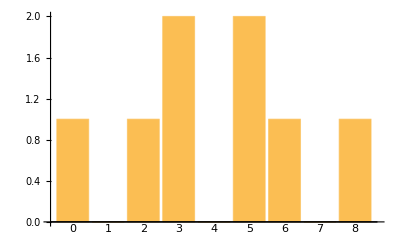

```mathematica
m=ms[[17]];m//MatrixForm
computeW[ms[[17]]]
computeW[ms[[17]]]//weightsHistorgram
```

```mathematica
(*genMat[{4,3,3,0,0}]//MatrixForm;*)

Clear[dispMatrixes];
dispMatrixes[ms_]:=Module[{ws,ws1,ws2,mfms,pics},
ws =computeW/@ms;
ws1 = Total[#[[;;,1]]]&/@ws;
ws2 = Total[#[[;;,2]]]&/@ws;
mfms=MatrixForm/@ms;
pics=weightsHistorgram/@ws;
GridBox[MapThread[Join,{List/@mfms,List/@ws1,List/@ws2,List/@pics}],GridBoxDividers->{"Rows"->{{True}}}]//DisplayForm
(*{ws}*)
]
```

```mathematica
t=Table[{i,j},{i,4,1,-1},{j,i,0,-1}];
ms=genMat[#]&/@Flatten[t,1];
```

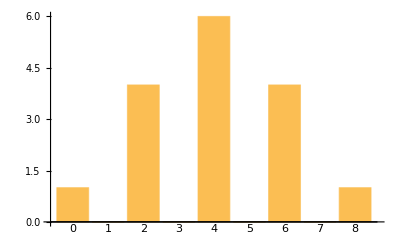
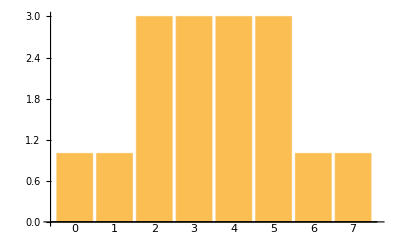
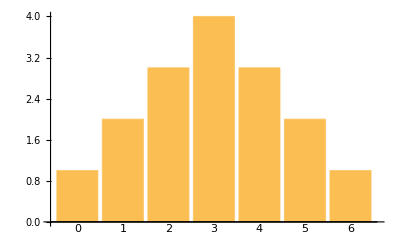
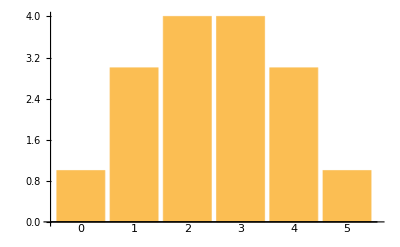
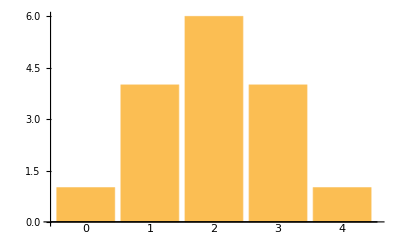
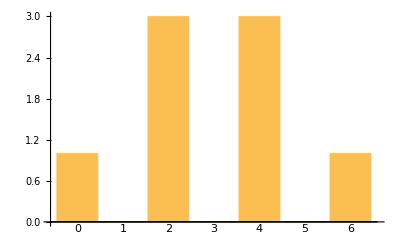
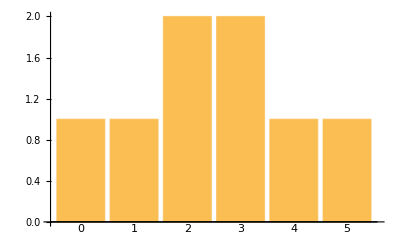
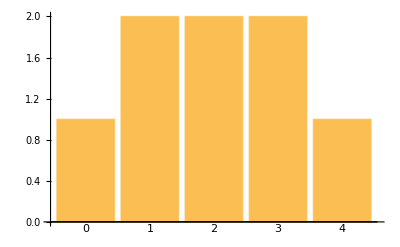
(1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1) | 36 | 16 | -Graphics-
(1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0) | 28 | 16 | -Graphics-
(1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0) | 21 | 16 | -Graphics-
(1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0) | 15 | 16 | -Graphics-
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | 10 | 16 | -Graphics-
(1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1) | 21 | 8 | -Graphics-
(1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0) | 15 | 8 | -Graphics-
(1 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0) | 10 | 8 | -Graphics-
(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | 6 | 8 | -Graphics-
(1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 0 | 0) | 10 | 4 | -Graphics-
(1 | 0 | 1
0 | 1 | 0
0 | 0 | 0) | 6 | 4 | -Graphics-
(1 | 0 | 0
0 | 1 | 0
0 | 0 | 0) | 3 | 4 | -Graphics-
(1 | 1 | 0
0 | 0 | 0
0 | 0 | 0) | 3 | 2 | -Graphics-
(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | 1 | 2 | -Graphics-

```mathematica
dispMatrixes[ms]
```

```mathematica
(* binomials precalculation *)
For[i=0,i≤ 1000,i++,
For[j=0,j≤ i,j++,
BINOM[i,j]=Binomial[i,j];(*&/@Range[0,n]*)
]
]
```

```mathematica
binomials[n_]:=Binomial[n,#]&/@Range[0,n]
binomials[n_]:=BINOM[n,#]&/@Range[0,n]
```

```mathematica
binomials[3]
```

{1,3,3,1}

```mathematica
(* calc *)
BxN[seq_,n_]:=Map[(PadRight[{#},n,0]&),seq]//Flatten//#[[;;-n]]&
```

```mathematica
BxN[{1,3,1},1]
BxN[{1,3,1},3]
```

{1,3,1}

{1,0,0,3,0,0,1}

```mathematica
totalSeq[sequences_]:=Module[{l=Max[Length/@sequences],res},
res=Array[0&,l];
(res+=PadRight[#,l,0])&/@sequences;
res
]
```

```mathematica
totalSeq[{{1,0,0,99},{2,100},{1}}]
```

{4,100,0,99}

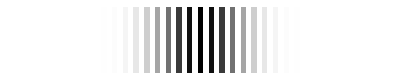

```mathematica
{BxN[binomials[30],2]}//ArrayPlot
```

```mathematica
(* sum histograms seq and seqx1, *)
totalSeqX[seq_,seqx1_]:=Module[{pos},
(*seqx1=Sign/@seqx;*)
pos=Position[seqx1,1]//Flatten;
seqx1[[pos]];
 PadLeft[seq,Length@seq+#-1,0]&/@pos //totalSeq
]
```

```mathematica
totalSeqX[binomials[10],binomials[1]]
binomials[11]
```

{1,11,55,165,330,462,462,330,165,55,11,1}

{1,11,55,165,330,462,462,330,165,55,11,1}

```mathematica
m=genMat[{4,4}];m//MatrixForm
tt=Total/@m
```

(1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1)

{2,2,2,2}

```mathematica
BxN[binomials[1],2]
```

{1,0,1}

```mathematica
histSumDiagonal[seq_]:=Module[{sequences},
sequences=BxN[binomials[1],#]&/@seq;
Fold[totalSeqX,sequences[[1]],sequences[[2;;]]]
]
```

```mathematica
histSumDiagonal[tt]
```

{1,0,4,0,6,0,4,0,1}

```mathematica
totalSeqX[{1,0,1},{1,1}]
totalSeqX[totalSeqX[{1,0,1},{1,1}],{1,1}]
```

{1,1,1,1}

{1,2,2,2,1}

```mathematica
histSumDiagonalOPT1[seq_]:=Module[{tally,elem,k,seq1,seq2,sequences,fold},
tally=SortBy[seq//Tally,Last];
{elem,k}=(Last@tally);

seq1=BxN[binomials[k],elem];
seq2=Select[seq,#≠elem&];
sequences={seq1}~Join~(BxN[binomials[1],#]&/@seq2);
fold=Fold[totalSeqX,sequences[[1]],sequences[[2;;]]]
(*{seq1,seq2,sequences,fold}*)
]
```

```mathematica
tt2={2,2,2,2}
histSumDiagonalOPT1[tt2]
histSumDiagonal[tt2]
```

{2,2,2,2}

{1,0,4,0,6,0,4,0,1}

{1,0,4,0,6,0,4,0,1}

```mathematica
(* test the speed for basis of 999 vectors *)
r1=AbsoluteTiming[Total/@genMat[{999,99}]//histSumDiagonal];
r2=AbsoluteTiming[Total/@genMat[{999,99}]//histSumDiagonalOPT1];
```

```mathematica
r1[[1]]
r2[[1]]
```

0.50763

0.16927

```mathematica
dispMatrixes2[ms_]:=Module[{ws,wsbin,mfms,pics},
ws =computeW/@ms;
wsbin=(histSumDiagonalOPT1[Total/@#])&/@ms;

mfms=MatrixForm/@ms;
pics=weightsHistorgram/@ws;
GridBox[MapThread[Join,{List/@mfms,List/@wsbin,List/@pics}],GridBoxDividers->{"Rows"->{{True}}}]//DisplayForm
(*{ws}*)
]
```

```mathematica
dispMatrixes3[ms_]:=Module[{ws,wsbin,mfms,pics},
ws =computeW/@ms;

mfms=MatrixForm/@ms;
pics=weightsHistorgram/@ws;
GridBox[MapThread[Join,{List/@mfms,List[#[[;;,2]]]&/@ws,List/@pics}],GridBoxDividers->{"Rows"->{{True}}}]//DisplayForm
(*{ws}*)
]
```

```mathematica
r1=AbsoluteTiming[Total/@genMat[{1},1,1]//histSumDiagonal]
```

{0.000181554,{1,1}}

```mathematica
histSumDiagonalOPT1[{2}]
```

{1,0,1}

```mathematica
ms[[-1]]
```

{{1,0,0},{0,0,0},{0,0,0}}

```mathematica
t=Table[{i,j,k},{i,4,1,-1},{j,i,0,-1},{k,j,0,-1}];
ms=genMat[#,1,1]&/@Flatten[t,2];
```

```mathematica
m=genMat[{16,10,4}];m//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
t1=AbsoluteTiming [computeW[m][[;;,2]] ]
t2=AbsoluteTiming [histSumDiagonal[Total/@m]]
t3=AbsoluteTiming [histSumDiagonalOPT1[Total/@m]]
t1[[1]]/t2[[1]]
t1[[1]]/t3[[1]]
```

{1.70411,{1,6,21,60,144,300,566,972,1536,2264,3114,4020,4897,5622,6105,6280,6105,5622,4897,4020,3114,2264,1536,972,566,300,144,60,21,6,1}}

{0.00116364,{1,6,21,60,144,300,566,972,1536,2264,3114,4020,4897,5622,6105,6280,6105,5622,4897,4020,3114,2264,1536,972,566,300,144,60,21,6,1}}

{0.000861761,{1,6,21,60,144,300,566,972,1536,2264,3114,4020,4897,5622,6105,6280,6105,5622,4897,4020,3114,2264,1536,972,566,300,144,60,21,6,1}}

1464.46

1977.48

```mathematica
histSumDiagonalOPT1[Total/@genMat[{4,4,4}]]
```

{1,0,0,4,0,0,6,0,0,4,0,0,1}

```mathematica
tupes=Tuples[Tuples[{0,1},2][[2;;]],4];
```

```mathematica
Length@tupes
```

81

```mathematica
tupes[[;;,;;,{1,2}]]
```

{{{0,1},{0,1},{0,1},{0,1}},{{0,1},{0,1},{0,1},{1,0}},{{0,1},{0,1},{0,1},{1,1}},{{0,1},{0,1},{1,0},{0,1}},{{0,1},{0,1},{1,0},{1,0}},{{0,1},{0,1},{1,0},{1,1}},{{0,1},{0,1},{1,1},{0,1}},{{0,1},{0,1},{1,1},{1,0}},{{0,1},{0,1},{1,1},{1,1}},{{0,1},{1,0},{0,1},{0,1}},{{0,1},{1,0},{0,1},{1,0}},{{0,1},{1,0},{0,1},{1,1}},{{0,1},{1,0},{1,0},{0,1}},{{0,1},{1,0},{1,0},{1,0}},{{0,1},{1,0},{1,0},{1,1}},{{0,1},{1,0},{1,1},{0,1}},{{0,1},{1,0},{1,1},{1,0}},{{0,1},{1,0},{1,1},{1,1}},{{0,1},{1,1},{0,1},{0,1}},{{0,1},{1,1},{0,1},{1,0}},{{0,1},{1,1},{0,1},{1,1}},{{0,1},{1,1},{1,0},{0,1}},{{0,1},{1,1},{1,0},{1,0}},{{0,1},{1,1},{1,0},{1,1}},{{0,1},{1,1},{1,1},{0,1}},{{0,1},{1,1},{1,1},{1,0}},{{0,1},{1,1},{1,1},{1,1}},{{1,0},{0,1},{0,1},{0,1}},{{1,0},{0,1},{0,1},{1,0}},{{1,0},{0,1},{0,1},{1,1}},{{1,0},{0,1},{1,0},{0,1}},{{1,0},{0,1},{1,0},{1,0}},{{1,0},{0,1},{1,0},{1,1}},{{1,0},{0,1},{1,1},{0,1}},{{1,0},{0,1},{1,1},{1,0}},{{1,0},{0,1},{1,1},{1,1}},{{1,0},{1,0},{0,1},{0,1}},{{1,0},{1,0},{0,1},{1,0}},{{1,0},{1,0},{0,1},{1,1}},{{1,0},{1,0},{1,0},{0,1}},{{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,1}},{{1,0},{1,0},{1,1},{0,1}},{{1,0},{1,0},{1,1},{1,0}},{{1,0},{1,0},{1,1},{1,1}},{{1,0},{1,1},{0,1},{0,1}},{{1,0},{1,1},{0,1},{1,0}},{{1,0},{1,1},{0,1},{1,1}},{{1,0},{1,1},{1,0},{0,1}},{{1,0},{1,1},{1,0},{1,0}},{{1,0},{1,1},{1,0},{1,1}},{{1,0},{1,1},{1,1},{0,1}},{{1,0},{1,1},{1,1},{1,0}},{{1,0},{1,1},{1,1},{1,1}},{{1,1},{0,1},{0,1},{0,1}},{{1,1},{0,1},{0,1},{1,0}},{{1,1},{0,1},{0,1},{1,1}},{{1,1},{0,1},{1,0},{0,1}},{{1,1},{0,1},{1,0},{1,0}},{{1,1},{0,1},{1,0},{1,1}},{{1,1},{0,1},{1,1},{0,1}},{{1,1},{0,1},{1,1},{1,0}},{{1,1},{0,1},{1,1},{1,1}},{{1,1},{1,0},{0,1},{0,1}},{{1,1},{1,0},{0,1},{1,0}},{{1,1},{1,0},{0,1},{1,1}},{{1,1},{1,0},{1,0},{0,1}},{{1,1},{1,0},{1,0},{1,0}},{{1,1},{1,0},{1,0},{1,1}},{{1,1},{1,0},{1,1},{0,1}},{{1,1},{1,0},{1,1},{1,0}},{{1,1},{1,0},{1,1},{1,1}},{{1,1},{1,1},{0,1},{0,1}},{{1,1},{1,1},{0,1},{1,0}},{{1,1},{1,1},{0,1},{1,1}},{{1,1},{1,1},{1,0},{0,1}},{{1,1},{1,1},{1,0},{1,0}},{{1,1},{1,1},{1,0},{1,1}},{{1,1},{1,1},{1,1},{0,1}},{{1,1},{1,1},{1,1},{1,0}},{{1,1},{1,1},{1,1},{1,1}}}

```mathematica
delSym[tupes0_]:=Module[{tupes=tupes0,i=1,tup,pos,len},
len = Length@tupes;
While[i≤ len,
tup=tupes[[i]];
pos = Position[tupes,tup[[;;,{2,1}]]]//Flatten;
(*Break[];*)
pos=Select[pos, #≠ i&];
tupes=tupes[[Complement[Range@Length@tupes,pos]]];
i++;
len = Length@tupes;
];
tupes
]
```

```mathematica
tupes2=delSym[tupes]
```

{{{0,1},{0,1},{0,1},{0,1}},{{0,1},{0,1},{0,1},{1,0}},{{0,1},{0,1},{0,1},{1,1}},{{0,1},{0,1},{1,0},{0,1}},{{0,1},{0,1},{1,0},{1,0}},{{0,1},{0,1},{1,0},{1,1}},{{0,1},{0,1},{1,1},{0,1}},{{0,1},{0,1},{1,1},{1,0}},{{0,1},{0,1},{1,1},{1,1}},{{0,1},{1,0},{0,1},{0,1}},{{0,1},{1,0},{0,1},{1,0}},{{0,1},{1,0},{0,1},{1,1}},{{0,1},{1,0},{1,0},{0,1}},{{0,1},{1,0},{1,0},{1,0}},{{0,1},{1,0},{1,0},{1,1}},{{0,1},{1,0},{1,1},{0,1}},{{0,1},{1,0},{1,1},{1,0}},{{0,1},{1,0},{1,1},{1,1}},{{0,1},{1,1},{0,1},{0,1}},{{0,1},{1,1},{0,1},{1,0}},{{0,1},{1,1},{0,1},{1,1}},{{0,1},{1,1},{1,0},{0,1}},{{0,1},{1,1},{1,0},{1,0}},{{0,1},{1,1},{1,0},{1,1}},{{0,1},{1,1},{1,1},{0,1}},{{0,1},{1,1},{1,1},{1,0}},{{0,1},{1,1},{1,1},{1,1}},{{1,1},{0,1},{0,1},{0,1}},{{1,1},{0,1},{0,1},{1,0}},{{1,1},{0,1},{0,1},{1,1}},{{1,1},{0,1},{1,0},{0,1}},{{1,1},{0,1},{1,0},{1,0}},{{1,1},{0,1},{1,0},{1,1}},{{1,1},{0,1},{1,1},{0,1}},{{1,1},{0,1},{1,1},{1,0}},{{1,1},{0,1},{1,1},{1,1}},{{1,1},{1,1},{0,1},{0,1}},{{1,1},{1,1},{0,1},{1,0}},{{1,1},{1,1},{0,1},{1,1}},{{1,1},{1,1},{1,1},{0,1}},{{1,1},{1,1},{1,1},{1,1}}}

```mathematica
Table[0,{i,0,4},{j,0,6}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
compMats[basem0_,ms_]:=Module[{bm=basem0,w,h,wl,hl,m,e,i,j=1,hi=1},
(* seq =~ {4,3,2,1} *)
{w,h}=Dimensions[basem0];
hi = 1;
For[i=1,i≤ Length@ms,i++,
{wl,hl}=Dimensions[ms[[i]]];

bm[[1;;wl,hi;;(hi+hl-1)]]=ms[[i]];
hi+=hl;
];
bm
]
```

```mathematica
tupes2[[1]]
```

{{0,1},{0,1},{0,1},{0,1}}

```mathematica
m1=Array[0&,{4,6}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
tupes[[1]]
```

{{0,1},{0,1},{0,1},{0,1}}

```mathematica
compMats[m1,{tupes2[[1]],tupes2[[2]],tupes2[[3]]}]//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1 | 1)

```mathematica
mats=compMats[Array[0&,{4,6}],{DiagonalMatrix[{1,1,1,1}],#}]&/@tupes2;
```

```mathematica
mats[[-1]]//MatrixForm
```

(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1)

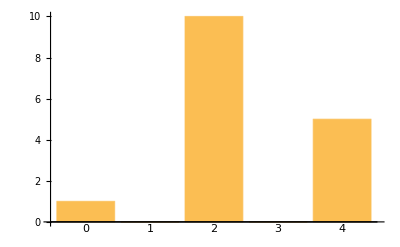
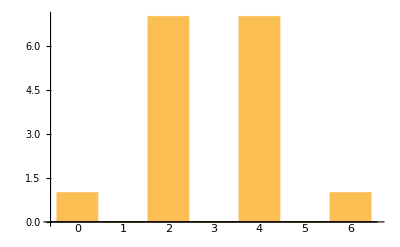
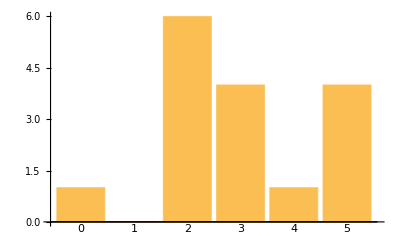
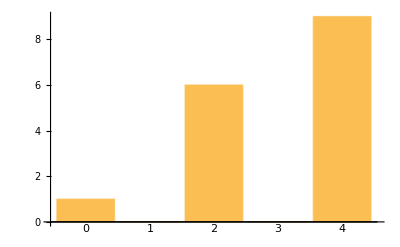
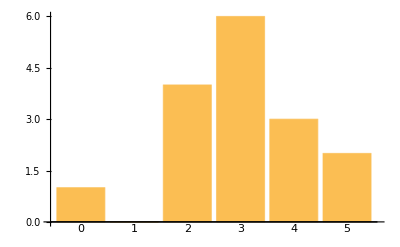
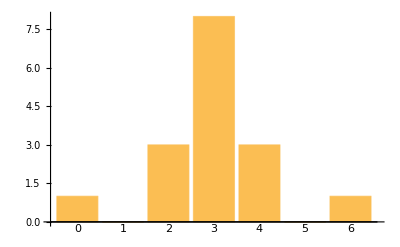
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1) | {1,0,10,0,5} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0) | {1,0,7,0,7,0,1} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1) | {1,0,6,4,1,4} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1) | {1,0,7,0,7,0,1} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0) | {1,0,6,0,9} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1) | {1,0,6,4,1,4} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1) | {1,0,7,0,7,0,1} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0) | {1,0,6,0,9} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1) | {1,0,6,0,9} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0) | {1,0,7,0,7,0,1} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1) | {1,0,3,8,3,0,1} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1) | {1,0,6,4,1,4} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1) | {1,0,3,8,3,0,1} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0) | {1,0,3,8,3,0,1} | -Graphics-
(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1) | {1,0,6,4,1,4} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1) | {1,0,3,8,3,0,1} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0) | {1,0,3,8,3,0,1} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0) | {1,0,3,8,3,0,1} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1) | {1,0,4,6,3,2} | -Graphics-
(1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1) | {1,0,6,4,1,4} | -Graphics-

```mathematica
dispMatrixes3[mats]
```

```mathematica
A=DiagonalMatrix[Array[1&,15]];
AN=FromDigits[#,2]&/@A
v=0;(*Array[0&,Length@A]*)
```

{16384,8192,4096,2048,1024,512,256,128,64,32,16,8,4,2,1}

```mathematica
(* Grey Code optimisation *)
Monitor[
Block[{len=Length@A,S,H,v=0},
H=Array[0&,1+Length@A];
H[[1]]=1;
S=Table[2^i,{i,0,len+1}];
For[i=0,i<2^len,i++,
For[j=1,j<len+1,j++,
If[i==S[[j]],
S[[j]]+=2^j;
v=BitXor[v,AN[[j]]];
H[[1+DigitCount[v,2,1] ]]++;
Break[];
];
];
];
H
],ProgressIndicator[i/2^Length@A]
]
```

{1,15,105,455,1365,3003,5005,6435,6435,5005,3003,1365,455,105,15,1}